## Math 137 Sp 19 Mathematica Hw 4 More volumes and the importance of polynomials Ernst

Form groups of two. Each member of the group must understand and be able to explain (in detail) all of the homework turned in. We allow you to work in groups so that you have someone with whom you can talk about your work in detail. This is not meant for group members to only do half of the work. 
Each group turns in one (stapled) printout at the beginning of class.

Due: Friday, April 5

#### 2D integrals ∫∫_R f[x,y]ⅆxⅆy for volume measurements

You can plot a surface z=f[x,y] like this:

```mathematica
Clear[f,x,y];
f[x_,y_] = 3.1 x^2+2.3 y^2;
{{a,b},{c,d}} = {{-2,3},{-1,4}};

surfaceplot = Plot3D[f[x,y],{x,a,b},{y,c,d}];
   
spacer = 0.2;
threedims = 
      Graphics3D[{
            {Blue,Line[{{a,0,0},{b,0,0}}]},
                    Text["x",{b + spacer,0,0}],
            {Blue,Line[{{0,c,0},{0,d,0}}]},
                    Text["y",{0, d + spacer,0}],
            {Blue,Line[{{0,0,0},{0,0,50}}]},
                    Text["z",{0,0,50 + spacer}]}];
                    
fplot = Show[surfaceplot,threedims,
        PlotRange->All]
```

-Graphics3D-

How do you use the double integral
       ∫∫_R f[x,y]ⅆxⅆy 
to measure the volume of the solid consisting of everything between the surface plotted above and the xy-plane?

Answer:

```mathematica
∫_a^b ∫_c^d f[x,y]ⅆyⅆx
```

430.

The volume of the solid measures out to 430 cubic units.

#### Why double integrals measure volume

What is the physical process that confirms that the double integral
       ∫∫_R f[x,y]ⅆxⅆy=∫_c^d ∫_a^b f[x,y]ⅆxⅆy
actually measures the volume of the solid described in part i)?

Answer:

Look at some slices of the solid consisting of everything between the surface plotted above and the xy-plane:

```mathematica
Clear[slice,x,y,t];
slice[y_]:=ParametricPlot3D[{x,y,0}+t {0,0,f[x,y]},{x,a,b},{t,0,1}];
jump=(d-c)/3;

Table[Show[fplot,slice[y]],{y,c,d,jump}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

Animate these.

The physical process of calculating 
       ∫_c^d ∫_a^b f[x,y]ⅆxⅆy 
involves two steps.
First step:
For each y with c≤y≤d, you calculate
       ∫_a^b f[x,y]ⅆx:

```mathematica
Clear[first,x,y];
first[y_]=∫_a^b f[x,y]ⅆx
```

36.1667+11.5 y^2

As y advances from c to d, first[y] measures the area of the slices that sweep out the solid. 
For instance,

```mathematica
first[3]
```

139.667

measures the area of this slice of the solid:

```mathematica
Show[fplot,slice[3]]
```

-Graphics3D-

Second step: 
Calculate ∫_c^d first[y]ⅆy=∫_c^d ∫_a^b f[x,y]ⅆxⅆy.
This second integral sums up the area measurements of the individual slices and measures the volume.

```mathematica
second=∫_c^d first[y]ⅆy
```

430.

Compare to Mathematica's calculation of
       ∫_c^d ∫_a^b f[x,y]ⅆxⅆy:

```mathematica
∫_c^d ∫_a^b f[x,y]ⅆxⅆy
```

430.

Bingo.

#### Trying to calculate ∫∫_R f[x,y]ⅆxⅆy when R isn't a rectangle

Here is a little region R on the xy-plane.

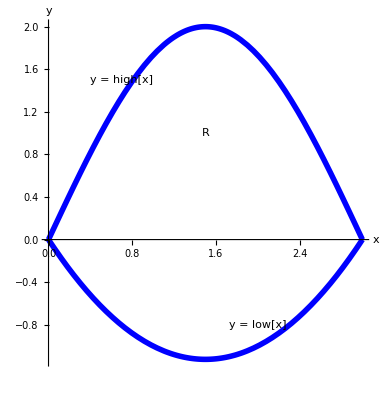

```mathematica
Clear[high,low,x];
high[x_]=2 Sin[(π x)/3];
low[x_]=1/2 x (x-3);

regionplot=Plot[{high[x],low[x]},{x,0,3},PlotStyle->{{Blue,Thickness[0.01]}},AspectRatio->Automatic,AxesLabel->{"x","y"},Epilog->{Text["y = high[x]",{0.7,1.5}],Text["y = low[x]",{2.0,-0.8}],Text["R",{1.5,1}]}]
```

The region R consists of all points between and on the plotted curves. Calculate
       ∫∫_R f[x,y]ⅆxⅆy
for
       f[x,y]=E^(-0.4x - 0.3y).

Answer:

Enter the function f[x,y]:

```mathematica
Clear[f,x,y];
f[x_,y_]=E^(-0.4 x-0.3 y)
```

To set up 
       ∫∫_R f[x,y]ⅆxⅆy
for calculation, you need a convenient way of slicing R.
Here's one:

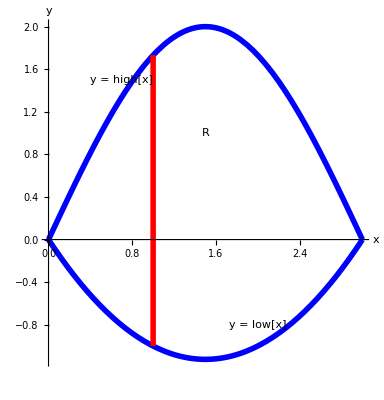

```mathematica
Clear[slice,sliceplot,x];
slice[x_]:=Graphics[{Red,Thickness[0.01],Line[{{x,low[x]},{x,high[x]}}]}];
sliceplot[x_]:=Show[regionplot,slice[x]];

Show[sliceplot[1]]
```

You slice from low to high, and this means that you integrate with respect to y first. This tells you how to set up
       ∫∫_R f[x,y]ⅆxⅆy=∫_0^3 (∫_low[x]^high[x] f[x,y]ⅆy)ⅆx 
for calculation:

```mathematica
Clear[first];
first[x_]=∫_low[x]^high[x] f[x,y]ⅆy
```

3.1 x^2 (-1/2 (-3+x) x+2 Sin[(π x)/3])+2.3 (-1/24 (-3+x)^3 x^3+8/3 Sin[(π x)/3]^3)

You can't use NIntegrate on the first integral 
because the formula for the first integral includes an x.
You can use NIntegrate on the second integral.

```mathematica
second=NIntegrate[first[x],{x,0,3}]
```

59.8282

Here's how to get Mathematica to calculate the double integral
       ∫∫_R f[x,y]ⅆxⅆy=∫_0^3 ∫_low[x]^high[x] f[x,y]ⅆyⅆx
in one sweet instruction with NIntegrate:

```mathematica
NIntegrate[f[x,y],{x,0,3},{y,low[x],high[x]}]
```

59.8282

Done.

Here is another little region on the xy-plane.

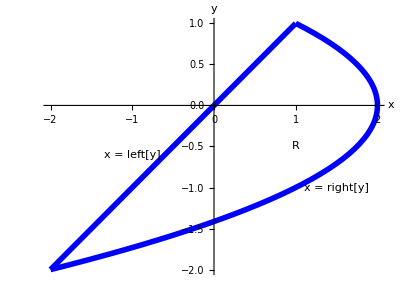

```mathematica
Clear[left,right,y];
left[y_]=y;
right[y_]=2-y^2;

regionplot=ParametricPlot[{{left[y],y},{right[y],y}},{y,-2,1},PlotStyle->{{Blue,Thickness[0.01]}},AspectRatio->Automatic,AxesLabel->{"x","y"},Epilog->{Text["x = left[y]",{-1,-0.6}],Text["x = right[y]",{1.5,-1}],Text["R",{1,-0.5}]}]
```

The region R consists of all points between and on the plotted curves. Calculate
       ∫∫_R f[x,y]ⅆxⅆy 
for
       f[x,y]=x y.

Answer:

Enter the function f[x,y]:

```mathematica
Clear[f,x,y];
f[x_,y_]=x y
```

To set up
       ∫∫_R f[x,y]ⅆxⅆy 
for calculation, you need a convenient way of slicing R.
Here's one:

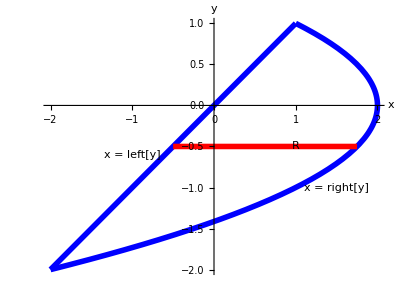

```mathematica
Clear[slice,sliceplot,y];
slice[y_]:=Graphics[{Red,Thickness[0.01],Line[{{left[y],y},{right[y],y}}]}];
sliceplot[y_]:=Show[regionplot,slice[y]];

Show[sliceplot[-0.5]]
```

You slice from left to right, and this means that you integrate with respect to x first. This tells you how to set up
       ∫∫_R f[x,y]ⅆxⅆy=∫_-2^1 ∫_left[y]^right[y] f[x,y]ⅆxⅆy 
for calculation:

```mathematica
Clear[first];
first[y_]=∫_left[y]^right[y] f[x,y]ⅆx
```

2.3 y^2 (2-y-y^2)+3.1 (-y^3/3+1/3 (2-y^2)^3)

You can't use NIntegrate on the first integral 
because the formula for the first integral includes an x.
You can use NIntegrate on the second integral.

```mathematica
second=∫_-2^1 first[x]ⅆx
```

20.5971

Here's how to get Mathematica to calculate the double integral
       ∫∫_R f[x,y]ⅆxⅆy=∫_-2^1 ∫_left[y]^right[y] f[x,y]ⅆxⅆy 
in one sweet instruction:

```mathematica
∫_-2^1 ∫_left[y]^right[y] f[x,y]ⅆxⅆy
```

20.5971

Done.

#### Part I Your Calculation of double integrals

(i) Here's a region R plotted in the xy-plane.

```mathematica
Clear[y];
Rplot=ParametricPlot[{{y (y-6)+1,y},{Cos[(π y)/6]^2,y}},{y,0,6},
		PlotStyle->{{Red,Thickness[0.01]}},AxesLabel->{"x","y"},Epilog->Text["R",{-4,3}]]
```

Go with 
       f[x,y]=y-x+3 
and calculate
       ∫∫_R f[x,y]ⅆxⅆy
by the method of least labor on your part.

(ii) Here's another region R plotted in the xy-plane.

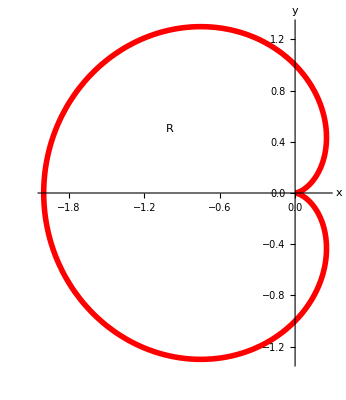

```mathematica
Clear[x,y,t];
x[t_]=Cos[t] (1-Cos[t]);
y[t_]=Sin[t] (1-Cos[t]);

Rplot=ParametricPlot[{x[t],y[t]},{t,0,2 π},
		PlotRange->All,PlotStyle->{{Red,Thickness[0.01]}},AxesLabel->{"x","y"},Epilog->Text["R",{-1,0.5}]]
```

```mathematica
Integrate[
```

Fancy dudes say that this is the cardiod described in polar coordinates
 by the polar equation r[t]=1-Cos[t].

Go with 
       f[x,y]=3+y-x
and calculate
       ∫∫_R f[x,y]ⅆxⅆy
by the method of least labor on your part.

Next, go with
       g[x,y]=3-x 
and calculate
       ∫∫_R g[x,y]ⅆxⅆy
by the method of least labor on your part.

Compare the values of
       ∫∫_R f[x,y]ⅆxⅆy and ∫∫_R g[x,y]ⅆxⅆy.
Discuss how you think that the shape and position of R account for the relationship between these two numbers.

(iii) Here is another region R plotted in the xy-plane.

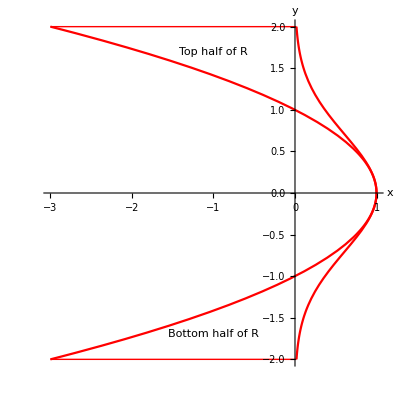

```mathematica
Clear[high,low,y];
xhigh[y_]=E^(-y^2);
xlow[y_]=1-y^2;

Rplot=ParametricPlot[{{xhigh[y],y},{xlow[y],y}},{y,-2,2},
		PlotStyle->Red, AxesLabel->{"x","y"},PlotRange->All,AspectRatio->Automatic,Epilog->{{Red,Line[{{xlow[-2],-2},{xhigh[-2],-2}}]},{Red,Line[{{xlow[2],2},{xhigh[2],2}}]},Text["Top half of R",{-1,1.7}],Text["Bottom half of R",{-1,-1.7}]}]
```

```mathematica
?Integrate
```

Integrate[f,x] gives the indefinite integral ∫f dx. 
Integrate[f,{x,x_min,x_max}] gives the definite integral ∫_x_min^x_max f dx. 
Integrate[f,{x,x_min,x_max},{y,y_min,y_max},…] gives the multiple integral ∫_x_min^x_max dx∫_y_min^y_max dy … f. 
Integrate[f,{x,y,…}∈reg] integrates over the geometric region reg.

```mathematica
Integrate
```

Go with 
       f[x,y]=y E^-x
       g[x,y]=y^2 E^-x and
       h[x,y]=y^3 E^-x 
and calculate
       ∫∫_R f[x,y]ⅆxⅆy,
       ∫∫_R g[x,y]ⅆxⅆy, and 
       ∫∫_R h[x,y]ⅆxⅆy
by the method of least labor on your part.
Look at the formulas for f[x,y] and g[x,y] and then look at the shape and position of R and explain why it was no surprise that
       ∫∫_R f[x,y]ⅆxⅆy and ∫∫_R h[x,y]ⅆxⅆy 
came out the way they did.

(iv) Here is another region R plotted in the xy-plane.

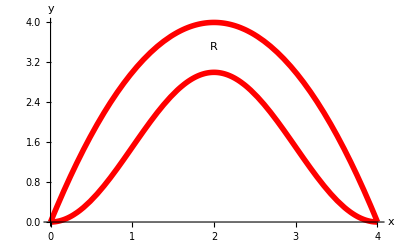

```mathematica
Clear[x,y,Rplot];
Rplot=Plot[{3 Sin[(π x)/4]^2,x (4-x)},{x,0,4},
		PlotStyle->{{Red,Thickness[0.01]}},AxesLabel->{"x","y"},Epilog->Text["R",{2,3.5}]]
```

Go with 
       f[x,y]=4x-y 
and calculate
       ∫∫_R f[x,y]ⅆxⅆy
by the method of least labor on your part.

(v) Given that the region R consists of everything inside the ellipse
       ((x+3)/7)^2+((y-1)/2)^2=1,
go with
       f[x,y]=x^2-3 y^2 
and calculate
       ∫∫_R f[x,y]ⅆxⅆy
by the method of least labor on your part.

#### Part II A. Getting Started

Pick a function, that involves a transcendental (trig functions, hyp. trig functions, logartihms, or exponentials).
Pick a number a
Compute the following:
y_1=f(a)+(-a+x) f'(a)
y_2=f(a)+(-a+x) f'(a)+1/2 (-a+x)^2 f''(a)
y_3=f(a)+(-a+x) f'(a)+1/2 (-a+x)^2 f''(a)+1/6 (-a+x)^3 f^(3)(a)
y_4=f(a)+(-a+x) f'(a)+1/2 (-a+x)^2 f''(a)+1/6 (-a+x)^3 f^(3)(a)+1/24 (-a+x)^4 f^(4)(a)
y_5=f(a)+(-a+x) f'(a)+1/2 (-a+x)^2 f''(a)+1/6 (-a+x)^3 f^(3)(a)+1/24 (-a+x)^4 f^(4)(a)+1/120 (-a+x)^5 f^(5)(a)
y_6=f(a)+(-a+x) f'(a)+1/2 (-a+x)^2 f''(a)+1/6 (-a+x)^3 f^(3)(a)+1/24 (-a+x)^4 f^(4)(a)+1/120 (-a+x)^5 f^(5)(a)+1/720 (-a+x)^6 f^(6)(a)
Plot the original function y=f(x) together with y_1,y_2,.....,y_6 in the interval [a-5,a+5] for some positive number h. What do you observe?

```mathematica
?D
```

```mathematica
a=4;
```

```mathematica
f[x_]:=Sin[x]
```

```mathematica
y1[x_]:=f[a]+(-a+x)f'[a]
y2[x_]:=y1[x]+1/2(-a+x)^2 f''[a]
y3[x_]:=y2[x]+1/6(-a+x)^3 f'''[a]
y4[x_]:=y3[x]+1/24(-a+x)^4 f''''[a]
y5[x_]:=y4[x]+1/120(-a+x)^5 f'''''[a]
y6[x_]:=y5[x]+1/720(-a+x)f''''''[a]
```

```mathematica
FunctionDomain[y1[x], x]
```

x<0||x>0

```mathematica
?PlotLegends
```

PlotLegends is an option for plot functions that specifies what legends to use.

General::ivar: 3 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

D::dvar: Multiple derivative specifier {3.,5.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

General::stop: Further output of D::dvar will be suppressed during this calculation.

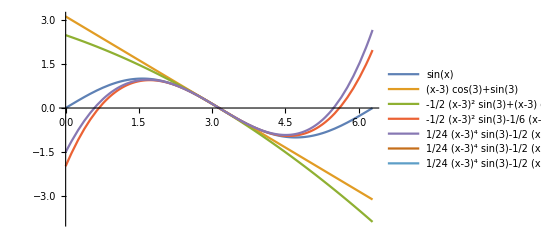

```mathematica
Plot[{f[x],y1[x],y2[x],y3[x],y4[x],y5[x],y6[x]}, {x,0, 2π}, PlotLegends->{f[x],y1[x],y2[x],y3[x],y4[x],y5[x],y6[x]}]
```

```mathematica
a:=3;
(*h:=3;*)
f[x_]:=Sin[x];
y1[x_]:= f[a]+(-a+x) f'[a]
y2[x_]:= f[a]+(-a+x) f'[a]+1/2 (-a+x)^2 f''[a];
y3[x_]:= f[a]+(-a+x) f'[a]+1/2 (-a+x)^2 f''[a]+1/6 (-a+x)^3 f'''[a];
y4[x_]:= f[a]+(-a+x) f'[a]+1/2 (-a+x)^2 f''[a]+1/6 (-a+x)^3 f'''[a]+1/24 (-a+x)^4 f''''[a];
y5[x_]= f[a]+(-a+x) f'[a]+1/2 (-a+x)^2 f''[a]+1/6 (-a+x)^3 f'''[a]+1/24 (-a+x)^4 f''''[a]+1/120(-a+x)^5 (D[f[x],{x,5}]/.x->a);
y6[x_]= f[a]+(-a+x) f'[a]+1/2 (-a+x)^2 f''[a]+1/6 (-a+x)^3 f'''[a]+1/24 (-a+x)^4 f''''[a]+1/120(-a+x)^5 (D[f[x],{x,5}]/.x->a)+1/720(-a+x)^6 (D[f[x],{x,6}]/.x->a);

Plot[{f[x],y1[x],y2[x],y3[x],y4[x],y5[x],y6[x]},{x,a-h,a+h},PlotLegends->{f[x],y1[x],y2[x],y3[x],y4[x],y5[x],y6[x]}]
```

Plot::plln: Limiting value 3-h in {Charting`Private`pvar$8898,3-h,3+h} is not a machine-sized real number.

Plot[{f[x],y1[x],y2[x],y3[x],y4[x],y5[x],y6[x]},{x,a-h,a+h},PlotLegends→{f[x],y1[x],y2[x],y3[x],y4[x],y5[x],y6[x]}]

#### Example

```mathematica
?D
```

D[f,x] gives the partial derivative ∂f/∂x. 
D[f,{x,n}] gives the multiple derivative ∂^n f/∂x^n.
D[f,x,y,…] gives the partial derivative ⋯ (∂/∂y)(∂/∂x) f.
D[f,{x,n},{y,m},…] gives the multiple partial derivative ⋯ (∂^m /∂y^m)(∂^n /∂x^n) f.
D[f,{{x_1,x_2,…}}] for a scalar f gives the vector derivative (∂f/∂x_1,∂f/∂x_2,…). 
D[f,{array}] gives an array derivative.

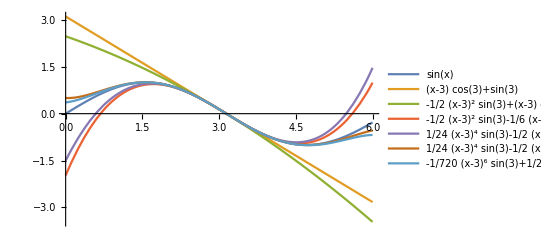

```mathematica
a:=3;
h:=3;
f[x_]:=Sin[x];
y1[x_]:= f[a]+(-a+x) f'[a]
y2[x_]:= f[a]+(-a+x) f'[a]+1/2 (-a+x)^2 f''[a];
y3[x_]:= f[a]+(-a+x) f'[a]+1/2 (-a+x)^2 f''[a]+1/6 (-a+x)^3 f'''[a];
y4[x_]:= f[a]+(-a+x) f'[a]+1/2 (-a+x)^2 f''[a]+1/6 (-a+x)^3 f'''[a]+1/24 (-a+x)^4 f''''[a];
y5[x_]= f[a]+(-a+x) f'[a]+1/2 (-a+x)^2 f''[a]+1/6 (-a+x)^3 f'''[a]+1/24 (-a+x)^4 f''''[a]+1/120(-a+x)^5 (D[f[x],{x,5}]/.x->a);
y6[x_]= f[a]+(-a+x) f'[a]+1/2 (-a+x)^2 f''[a]+1/6 (-a+x)^3 f'''[a]+1/24 (-a+x)^4 f''''[a]+1/120(-a+x)^5 (D[f[x],{x,5}]/.x->a)+1/720(-a+x)^6 (D[f[x],{x,6}]/.x->a);

Plot[{f[x],y1[x],y2[x],y3[x],y4[x],y5[x],y6[x]},{x,a-h,a+h},PlotLegends->{f[x],y1[x],y2[x],y3[x],y4[x],y5[x],y6[x]}]
```

#### B. Generalize

The functions y_i follow a pattern. What is that pattern?
Write down the general formula for the pattern.
Write a function uPoly[f,n,a,h] that given a positive integer n,  a number a, a number h, and a function y=f(x) computes the function y_n and plots the functions f(x) and y_n together over the interval [a-h,a+h]. 
The function should be red and thick and the polynomial should be blue and not quite so thick.
Give three examples of different functions to show that your code works.
Two examples:

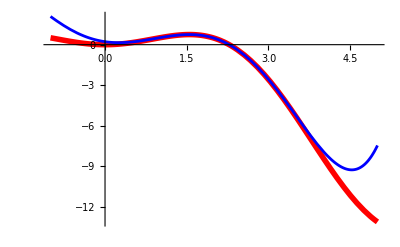

```mathematica
f[x_]:=x Sin[x]-x^2/3
uPoly[f,5,2,3]
```

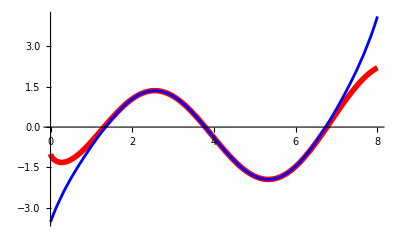

```mathematica
f[x_]:=Log[x] Sin[x]-Cos[x]
uPoly[f,8,4,4]
```

#### C. More examples using the function you generated in part II B.

a) Use the function f(x)=x tan(x/6)-x/ⅇ^(x/5)+√(ln(x+12)) with a=0 and h=8.
Find a value of n large enough that when you call the uPoly function you see no difference between the the two graphs. If this is not possible then show you best attempt and explain what you observe. If it is not possible, explain why you think this is not possible.

b) Use the function f(x)=x cos(sin(x))-ⅇ^(.02x) with a=5 and h=3.
Find a value of n large enough that when you call the uPoly function you see no difference between the the two graphs.  If this is not possible then show you best attempt and explain what you observe. If it is not possible, explain why you think this is not possible. 

c) Use the function f(x)=ln(x)-ⅇ^(.02x) with a=2 and h=3.
Find a value of n large enough that when you call the uPoly function you see no difference between the the two graphs.  If this is not possible then show you best attempt and explain what you observe. If it is not possible, explain why you think this is not possible. 

d) Use the function f(x)=1/(x^2+5) with a=1 and h=5.
Find a value of n large enough that when you call the uPoly function you see no difference between the the two graphs.  If this is not possible then show you best attempt and explain what you observe. If it is not possible, explain why you think this is not possible.

e) Use the function f(x)=1/100 x^6-3/100 x^5+1/20 x^4-1/10 x^3+1/5 x^2+x-100
Compute the functions y_1,y_2,y_(3,.....) y_(n,...). Choose any a-value you like and simplify you answer for each function.
What do you observe?

#### D. Approximate two values of trig functions

For a suitable choice of a, we can evaluate trig-functions without difficulty, examples are a=0, π/6, π/4...

a) You want to compute sin(2) with a forty digits of precision
Use one of the functions y_1,y_2,y_(3,.....) y_(n,...) with a suitable a-value of your choice to compute cos(2) with this precision.
Here because of your choice of a this can be done in principle using only addition/subtraction/multiplication/division.
How do you know that you have the desired precision?

b) You want to compute cos(10) with a fifty digits of precision
Use one of the functions y_1,y_2,y_(3,.....) y_(n,...) with a suitable a-value of your choice to compute sin(10) with this precision.
Here because of your choice of a this can be done in principle using only addition/subtraction/multiplication/division.
How do you know that you have the desired precision?